```mathematica
RotationsE1[alpha_]:=Module[{Re1},
Re1= {{1,0,0},{0,Cos[alpha Degree], -Sin[alpha Degree]}, {0,Sin[alpha Degree],Cos[alpha Degree]}};
Return[Re1]
];
```

```mathematica
RotationsE2[alpha_]:=Module[{Re2},
Re2 = {{Cos[alpha Degree],0,Sin[alpha Degree]},{0,1,0},{-Sin[alpha Degree],0, Cos[alpha Degree]}};
Return[Re2]
];
```

```mathematica
RotationsE3[alpha_]:=Module[{Re3},
Re3 = {{Cos[alpha Degree],-Sin[alpha Degree],0},{Sin[alpha Degree], Cos[alpha Degree],0},{0,0,1}};
Return[Re3]
];

ComputePointsFromRotatedCamera[WorldPoints_,Rotation_,Rotation2_,zeta_,e_,e2_]:=Module[{T,T2,Oc2Points,OcPoints,Tt,Tt2,ProjectionMtx,eOc,eOcNotRot,e2OcNotRot,e2Oc},

T= {{Rotation[[1,1]],Rotation[[1,2]],Rotation[[1,3]],0},{Rotation[[2,1]],Rotation[[2,2]],Rotation[[2,3]],0},{Rotation[[3,1]],Rotation[[3,2]],Rotation[[3,3]],0},{0,0,0,1}};

Print["T =", T];

Tt= Transpose[T];
Print["Tt =", Tt];

T2= {{Rotation2[[1,1]],Rotation2[[1,2]],Rotation2[[1,3]],0},{Rotation2[[2,1]],Rotation2[[2,2]],Rotation2[[2,3]],0},{Rotation2[[3,1]],Rotation2[[3,2]],Rotation2[[3,3]],0},{0,0,0,1}};
Print["T2 =", T2];

Tt2=T2.T;
Print["Tt2 =", Tt2];
Tt2 = Transpose[Tt2];

Print["Tt2 =", Tt2];

Oc2Points=ConstantArray[0,{4,4}];
Oc2Points[[All,1]]= Tt2.WorldPoints[[All,1]];
Oc2Points[[All,2]]=Tt2.WorldPoints[[All,2]];
Oc2Points[[All,3]]=Tt2.WorldPoints[[All,3]];
Oc2Points[[All,4]]=Tt2.WorldPoints[[All,4]];

(*Print[
"OcPoints",ListPlot[ {Oc2Points[[All,1]][[1;;2]], Oc2Points[[All,2]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,4]][[1;;2]]  }
]
];*)

Print["Oc2Points = ",MatrixForm[Oc2Points]];
Print["Oc2Points = ",MatrixForm[Rationalize[N[Oc2Points]]]];

OcPoints=ConstantArray[0,{4,4}];
OcPoints[[All,1]]= Tt.WorldPoints[[All,1]];
OcPoints[[All,2]]=Tt.WorldPoints[[All,2]];
OcPoints[[All,3]]=Tt.WorldPoints[[All,3]];
OcPoints[[All,4]]=Tt.WorldPoints[[All,4]];

Print["OcPoints = ",MatrixForm[OcPoints]];
Print["OcPoints = ",MatrixForm[Rationalize[N[OcPoints]]]];
Print[
"OcPoints = ",ListPlot[ {OcPoints[[All,1]][[1;;2]], OcPoints[[All,2]][[1;;2]],OcPoints[[All,3]][[1;;2]],OcPoints[[All,4]][[1;;2]]  }
]
];



ProjectionMtx = {{zeta,0,0,0},{0,zeta,0,0},{0,0,zeta,0},
{0,0,1,0}};

Oc2Points = ProjectionMtx.Oc2Points;

Oc2Points[[All,1]]= Oc2Points[[All,1]]/Oc2Points[[4,1]];
Oc2Points[[All,2]]= Oc2Points[[All,2]]/Oc2Points[[4,2]];
Oc2Points[[All,3]]= Oc2Points[[All,3]]/Oc2Points[[4,3]];
Oc2Points[[All,4]]= Oc2Points[[All,4]]/Oc2Points[[4,4]];
Print["Projected Oc2Points = ",MatrixForm[Rationalize[N[Oc2Points]]]];


OcPoints = ProjectionMtx.OcPoints;

OcPoints[[All,1]]= OcPoints[[All,1]]/OcPoints[[4,1]];
OcPoints[[All,2]]= OcPoints[[All,2]]/OcPoints[[4,2]];
OcPoints[[All,3]]= OcPoints[[All,3]]/OcPoints[[4,3]];
OcPoints[[All,4]]= OcPoints[[All,4]]/OcPoints[[4,4]];
Print["Projected OcPoints = ",MatrixForm[Rationalize[N[OcPoints]]]];

(*Berechnung der beiden e einmal in der ebene = e und einal außerhalb dder Ebene e2*)
eOc=Tt.e;
eOcNotRot = Tt2.e;

e2Oc = Tt.e2;
e2OcNotRot= Tt2.e2;


(*Berechnung von e in der Ebene*)
eOc=ProjectionMtx.eOc;
eOc=eOc/eOc[[4]];
eOcNotRot = ProjectionMtx.eOcNotRot;
eOcNotRot = eOcNotRot/eOcNotRot[[4]];
Print["eOc = ",MatrixForm[Rationalize[N[ eOc]]]];
Print["eOcNotRot  = ",MatrixForm[Rationalize[N[ eOcNotRot ]]]];

Print[
"Projected Oc2Points = ",Show[ListPlot[ {Oc2Points[[All,1]][[1;;2]], Oc2Points[[All,2]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,4]][[1;;2]],eOc[[1;;2]]  }],
ListLinePlot[{Oc2Points[[All,1]][[1;;2]],Oc2Points[[All,4]][[1;;2]],Oc2Points[[All,3]][[1;;2]],Oc2Points[[All,2]][[1;;2]]}]
]
];



Print[
"Projected OcPoints = ",ListPlot[ {OcPoints[[All,1]][[1;;2]], OcPoints[[All,2]][[1;;2]],OcPoints[[All,3]][[1;;2]],OcPoints[[All,4]][[1;;2]],eOcNotRot[[1;;2]]  }
]
];

(*Berechnung von e2 welches nicht in der Ebene der anderen Punkte liegt*)

e2Oc = ProjectionMtx.e2Oc;
e2Oc=e2Oc/e2Oc[[4]];

e2OcNotRot = ProjectionMtx.e2OcNotRot;
e2OcNotRot = e2OcNotRot/e2OcNotRot[[4]];
Print["e2Oc = ",MatrixForm[Rationalize[N[e2Oc]]]];
Print["e2OcNotRot = ",MatrixForm[Rationalize[N[e2OcNotRot]]]];

ComputeHomography[WorldPoints,Oc2Points,OcPoints,eOc,e2Oc,eOcNotRot,e2OcNotRot ];

];

ComputeHomography[WorldPoints_,Oc2Points_,OcPoints_,eOc_,e2Oc_,eOcNotRot_,e2OcNotRot_]:=Module[{H,OcTestPointsH,Oc2TestPointsH,eOcTestPointsH,e2OcTestPointsH,CoefficientMtx,nullspace,Oc2PointsOfHomography,OcPointsOfHomography,eOcPointsOfHomography,e2OcPointsOfHomography},

CoefficientMtx= ConstantArray[0,{8,9}];
CoefficientMtx[[1]]=
{OcPoints[[1,1]],OcPoints[[2,1]],1,0,0,0,-OcPoints[[1,1]]*Oc2Points[[1,1]],-OcPoints[[2,1]]*Oc2Points[[1,1]],-Oc2Points[[1,1]]};
CoefficientMtx[[2]]=
{0,0,0,OcPoints[[1,1]],OcPoints[[2,1]],1,-OcPoints[[1,1]]*Oc2Points[[2,1]],-OcPoints[[2,1]]*Oc2Points[[2,1]],-Oc2Points[[2,1]]};
CoefficientMtx[[3]]=
{OcPoints[[1,2]],OcPoints[[2,2]],1,0,0,0,-OcPoints[[1,2]]*Oc2Points[[1,2]],-OcPoints[[2,2]]*Oc2Points[[1,2]],-Oc2Points[[1,2]]};
CoefficientMtx[[4]]=
{0,0,0,OcPoints[[1,2]],OcPoints[[2,2]],1,-OcPoints[[1,2]]*Oc2Points[[2,2]],-OcPoints[[2,2]]*Oc2Points[[2,2]],-Oc2Points[[2,2]]};
CoefficientMtx[[5]]=
{OcPoints[[1,3]],OcPoints[[2,3]],1,0,0,0,-OcPoints[[1,3]]*Oc2Points[[1,3]],-OcPoints[[2,3]]*Oc2Points[[1,3]],-Oc2Points[[1,3]]};
CoefficientMtx[[6]]=
{0,0,0,OcPoints[[1,3]],OcPoints[[2,3]],1,-OcPoints[[1,3]]*Oc2Points[[2,3]],-OcPoints[[2,3]]*Oc2Points[[2,3]],-Oc2Points[[2,3]]};
CoefficientMtx[[7]]=
{OcPoints[[1,4]],OcPoints[[2,4]],1,0,0,0,-OcPoints[[1,4]]*Oc2Points[[1,4]],-OcPoints[[2,4]]*Oc2Points[[1,4]],-Oc2Points[[1,4]]};
CoefficientMtx[[8]]=
{0,0,0,OcPoints[[1,4]],OcPoints[[2,4]],1,-OcPoints[[1,4]]*Oc2Points[[2,4]],-OcPoints[[2,4]]*Oc2Points[[2,4]],-Oc2Points[[2,4]]};

(*Print["CoefficientMtx = ", MatrixForm[CoefficientMtx]]*)

Print["Rank = ", MatrixRank[CoefficientMtx]];
Print["CoefficientMtx = ", MatrixForm[Rationalize[N[CoefficientMtx]]]];

nullspace = NullSpace[CoefficientMtx];
Print["NullSpace = ",MatrixForm[nullspace] ];

H={{nullspace[[1,1]],nullspace[[1,2]],nullspace[[1,3]]},{nullspace[[1,4]],nullspace[[1,5]],nullspace[[1,6]]},{nullspace[[1,7]],nullspace[[1,8]],nullspace[[1,9]]}};
Print["H = ",MatrixForm[Simplify[N [H]]]];
Print["H = ",MatrixForm[Simplify[N [Inverse[H]]]]];

OcTestPointsH = {{OcPoints[[1,1]],OcPoints[[1,2]],OcPoints[[1,3]],OcPoints[[1,4]]},{OcPoints[[2,1]],OcPoints[[2,2]],OcPoints[[2,3]],OcPoints[[2,4]]},
{1,1,1,1}};
Oc2TestPointsH = {{Oc2Points[[1,1]],Oc2Points[[1,2]],Oc2Points[[1,3]],Oc2Points[[1,4]]},{Oc2Points[[2,1]],Oc2Points[[2,2]],Oc2Points[[2,3]],Oc2Points[[2,4]]},
{1,1,1,1}};

Oc2PointsOfHomography = H.OcTestPointsH;

Print["Oc2PointsOfHomography = ", MatrixForm[Rationalize[N[Oc2PointsOfHomography]]]];

For[i = 1, i≤ 3,i++,
Oc2PointsOfHomography [[All,i]]=Oc2PointsOfHomography [[All,i]]/Oc2PointsOfHomography [[3,i]];
];
Print["Oc2PointsOfHomography = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography]]]];

OcPointsOfHomography= Inverse[H].Oc2TestPointsH;
(*OcPointsOfHomography=Map[#/#[[3]]&,OcPointsOfHomography];*)
Print["OcPointsOfHomography= ", MatrixForm[Rationalize[N[OcPointsOfHomography]]]];
For[i = 1, i≤ 3,i++,
OcPointsOfHomography[[All,i]]=OcPointsOfHomography[[All,i]]/OcPointsOfHomography[[3,i]];
];
Print["OcPointsOfHomography= ", MatrixForm[Rationalize[N[OcPointsOfHomography]]]];


If[Oc2PointsOfHomography[[3,1]]≠0, Print["Oc2PointsOfHomography A = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,1]]/Oc2PointsOfHomography[[3,1]]]]]],Print["Oc2PointsOfHomography A = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,1]]]]]]];

If[Oc2PointsOfHomography[[3,2]]≠0, Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,2]]/Oc2PointsOfHomography[[3,2]]]]]],Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,2]]]]]]];

If[Oc2PointsOfHomography[[3,3]]≠0, Print["Oc2PointsOfHomography C = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,3]]/Oc2PointsOfHomography[[3,3]]]]]],Print["Oc2PointsOfHomography B = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,3]]]]]]];

If[Oc2PointsOfHomography[[3,4]]≠0, Print["Oc2PointsOfHomography D = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,4]]/Oc2PointsOfHomography[[3,4]]]]]],Print["Oc2PointsOfHomography D = ",MatrixForm[ Rationalize[N[Oc2PointsOfHomography[[All,4]]]]]]];



(*Berechnung des Punktes e in der Ebene mit der gleichen H wie die 4 restlichen Punkte*)
eOcTestPointsH = {eOcNotRot [[1]],eOcNotRot [[2]],1};
eOcPointsOfHomography = H.eOcTestPointsH;
Print["eOcPointsOfHomography = ", MatrixForm[Rationalize[N[eOcPointsOfHomography ]]]];
If[eOcPointsOfHomography[[3]]≠0, Print["eOcPointsOfHomography E = ",MatrixForm[Rationalize[N[eOcPointsOfHomography/eOcPointsOfHomography[[3]]]]]],Print["eOcPointsOfHomography E = ",MatrixForm[Rationalize[N[eOcPointsOfHomography]]]]];

(*Berechnung des Punktes e welcher nicht in der Ebene liegt mit der gleichen H wie die 4 restlichen Punkte und e in der Ebene*)
e2OcTestPointsH = {e2OcNotRot[[1]],e2OcNotRot[[2]],1};
e2OcPointsOfHomography = H.e2OcTestPointsH;
Print["e2OcPointsOfHomography = ", MatrixForm[Rationalize[N[e2OcPointsOfHomography ]]]];
If[e2OcPointsOfHomography[[3]]≠0, Print["e2OcPointsOfHomography E2 = ",MatrixForm[Rationalize[N[e2OcPointsOfHomography/e2OcPointsOfHomography[[3]]]]]],Print["eOcPointsOfHomography E2 = ",MatrixForm[Rationalize[N[e2OcPointsOfHomography]]]]];

];
```

T ={{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}}

Tt ={{-1,0,0,0},{0,-1,0,0},{0,0,1,0},{0,0,0,1}}

T2 ={{1/(√2),0,1/(√2),0},{0,1,0,0},{-1/(√2),0,1/(√2),0},{0,0,0,1}}

Tt2 ={{-1/(√2),0,1/(√2),0},{0,-1,0,0},{1/(√2),0,1/(√2),0},{0,0,0,1}}

Tt2 ={{-1/(√2),0,1/(√2),0},{0,-1,0,0},{1/(√2),0,1/(√2),0},{0,0,0,1}}

Oc2Points = (√2 | -1/(√2)+√2 | -1/(√2)+√2 | √2
0 | 0 | -1 | -1
√2 | 1/(√2)+√2 | 1/(√2)+√2 | √2
1 | 1 | 1 | 1)

Oc2Points = (1.41421 | 0.707107 | 0.707107 | 1.41421
0 | 0 | -1 | -1
1.41421 | 2.12132 | 2.12132 | 1.41421
1 | 1 | 1 | 1)

OcPoints = (0 | -1 | -1 | 0
0 | 0 | -1 | -1
2 | 2 | 2 | 2
1 | 1 | 1 | 1)

OcPoints = (0 | -1 | -1 | 0
0 | 0 | -1 | -1
2 | 2 | 2 | 2
1 | 1 | 1 | 1)

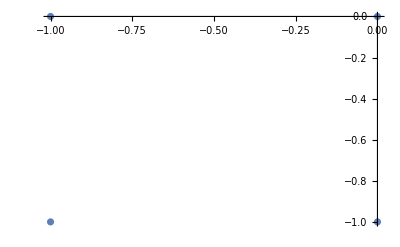
OcPoints = -Graphics-

Projected Oc2Points = (-1 | -1/3 | -1/3 | -1
0 | 0 | 0.471405 | 0.707107
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

Projected OcPoints = (0 | 1/2 | 1/2 | 0
0 | 0 | 1/2 | 1/2
-1 | -1 | -1 | -1
1 | 1 | 1 | 1)

eOc = (1/4
1/4
-1
1)

eOcNotRot  = (-3/5
0.282843
-1
1)

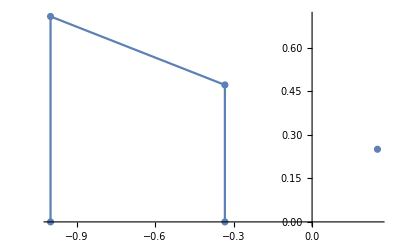
Projected Oc2Points = -Graphics-

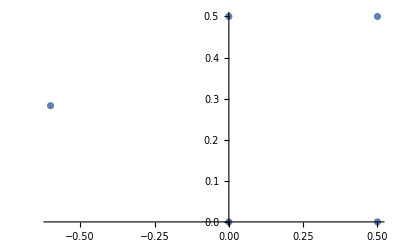
Projected OcPoints = -Graphics-

e2Oc = (-2/3
-2/3
-1
1)

e2OcNotRot = (-5
-2.82843
-1
1)

Rank = 8

CoefficientMtx = (0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1/2 | 0 | 1 | 0 | 0 | 0 | 1/6 | 0 | 1/3
0 | 0 | 0 | 1/2 | 0 | 1 | 0 | 0 | 0
1/2 | 1/2 | 1 | 0 | 0 | 0 | 1/6 | 1/6 | 1/3
0 | 0 | 0 | 1/2 | 1/2 | 1 | -0.235702 | -0.235702 | -0.471405
0 | 1/2 | 1 | 0 | 0 | 0 | 0 | 1/2 | 1
0 | 0 | 0 | 0 | 1/2 | 1 | 0 | -0.353553 | -0.707107)

NullSpace = (1 | 0 | -1 | 0 | √2 | 0 | 1 | 0 | 1)

H = (1. | 0. | -1.
0. | 1.41421 | 0.
1. | 0. | 1.)

H = (0.5 | 0. | 0.5
0. | 0.707107 | 0.
-0.5 | 0. | 0.5)

Oc2PointsOfHomography = (-1 | -1/2 | -1/2 | -1
0 | 0 | 0.707107 | 0.707107
1 | 3/2 | 3/2 | 1)

Oc2PointsOfHomography = (-1 | -1/3 | -1/3 | -1
0 | 0 | 0.471405 | 0.707107
1 | 1 | 1 | 1)

OcPointsOfHomography= (0 | 1/3 | 1/3 | 0
0 | 0 | 1/3 | 1/2
1 | 2/3 | 2/3 | 1)

OcPointsOfHomography= (0 | 1/2 | 1/2 | 0
0 | 0 | 1/2 | 1/2
1 | 1 | 1 | 1)

Oc2PointsOfHomography A = (-1
0
1)

Oc2PointsOfHomography B = (-1/3
0
1)

Oc2PointsOfHomography C = (-1/3
0.471405
1)

Oc2PointsOfHomography D = (-1
0.707107
1)

eOcPointsOfHomography = (-8/5
2/5
2/5)

eOcPointsOfHomography E = (-4
1
1)

e2OcPointsOfHomography = (-6
-4
-4)

e2OcPointsOfHomography E2 = (3/2
1
1)

```mathematica
alpha=180;
beta = 45;
a={0,0,2,1};
b={1,0,2,1};
c={1,1,2,1};
d={0,1,2,1};
e={0.5,0.5,2,1};
e2={4,4,-6,1};
Oc={0,0,0,1};
zeta= -1;
WorldPoints={{a[[1]],b[[1]],c[[1]],d[[1]]},{a[[2]],b[[2]],c[[2]],d[[2]]},{a[[3]],b[[3]],c[[3]],d[[3]]},{a[[4]],b[[4]],c[[4]],d[[4]]}};
ComputePointsFromRotatedCamera[WorldPoints,RotationsE3[alpha],RotationsE2[beta],zeta,e,e2];
```